```mathematica
AllGraphs[n_]:=Block[{edges=Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsets[Range[n],{2}]]},
Table[
Graph[Range[n],e, VertexLabels->"Name"]
,{e,Subsets[edges]}
]
]
```

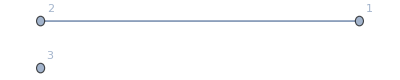
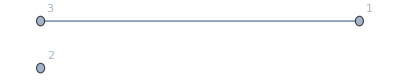
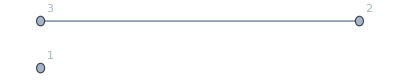
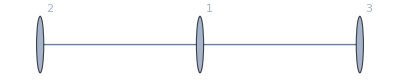
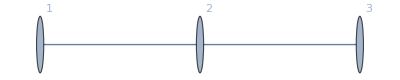
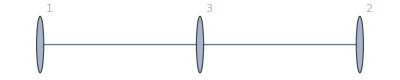
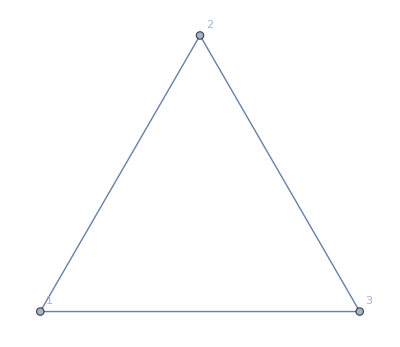
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllGraphs[3]
```

```mathematica
FindPartitions[g_]:=Sort[DeleteDuplicates[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula[g]]]]
```

```mathematica
VertexCount[JacobsThalGraph[3]]
```

7

```mathematica
FindPartitions2[g_]:=Tally[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula[g]]]
```

```mathematica
FindPartitions[JacobsThalGraph[3]]
```

{{{1,1,1,1,1,1,1},1},{{2,1,1,1,1,1},6},{{2,2,1,1,1},10},{{2,2,2,1},5}}

```mathematica
VertexCount[MinimalGraph[3]]
```

4

```mathematica
Table[VertexCount[ReadGrof[k]],{k,100}]
```

{4,5,6,6,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
Table[FindPartitions[ReadGrof[k]],{k,3,4}]
```

{{{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}},{{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}}

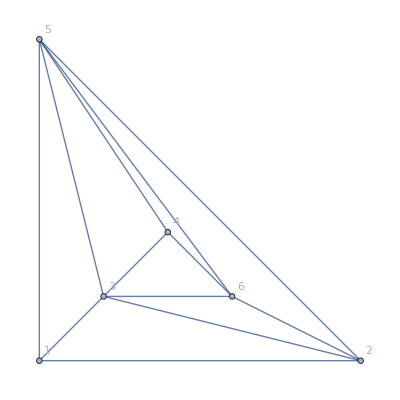

```mathematica
Graph[ReadGrof[3],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
SixNodes=
```

```mathematica
Flatten[Table[FindPartitions[ReadGrof[k]],{k,5,9}],1]//Tally
```

{{{2,2,2,1},4},{{2,2,1,1,1},5},{{2,1,1,1,1,1},5},{{1,1,1,1,1,1,1},5},{{3,2,1,1},1},{{3,1,1,1,1},2}}

```mathematica
FindPartitions2[MinimalGraph[5]]
```

{{{1,1,1,1,1,1},1},{{2,1,1,1,1},3},{{2,2,1,1},1}}

```mathematica
Flatten[Table[FindPartitions[MinimalGraph2[6]],{k,1,10}],1]//Tally
```

{{{2,2,2,1},7},{{2,2,1,1,1},10},{{2,1,1,1,1,1},10},{{1,1,1,1,1,1,1},10},{{3,2,1,1},3},{{3,1,1,1,1},3}}

```mathematica
FindPartitions2[JacobsThalGraph[2]]
```

{{{1,1,1,1,1,1},1},{{2,1,1,1,1},3},{{2,2,1,1},3},{{2,2,2},1}}

```mathematica
FindPartitions[JacobsThalGraph[4]]
```

{{3,3,2},{2,2,2,2},{3,2,2,1},{3,3,1,1},{2,2,2,1,1},{3,2,1,1,1},{2,2,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
Table[VertexCount[JacobsThalGraph[k]],{k,1,10}]
```

{5,6,7,8,9,10,11,12,13,14}

```mathematica
FindPartitions[JacobsThalGraph[10]]
```

{{6,6,2},{4,4,4,2},{5,4,3,2},{5,5,2,2},{6,3,3,2},{6,4,2,2},{6,5,2,1},{6,6,1,1},{3,3,3,3,2},{4,3,3,2,2},{4,4,2,2,2},{4,4,3,2,1},{4,4,4,1,1},{5,3,2,2,2},{5,3,3,2,1},{5,4,2,2,1},{5,4,3,1,1},{5,5,2,1,1},{6,2,2,2,2},{6,3,2,2,1},{6,3,3,1,1},{6,4,2,1,1},{6,5,1,1,1},{3,3,2,2,2,2},{3,3,3,2,2,1},{3,3,3,3,1,1},{4,2,2,2,2,2},{4,3,2,2,2,1},{4,3,3,2,1,1},{4,4,2,2,1,1},{4,4,3,1,1,1},{5,2,2,2,2,1},{5,3,2,2,1,1},{5,3,3,1,1,1},{5,4,2,1,1,1},{5,5,1,1,1,1},{6,2,2,2,1,1},{6,3,2,1,1,1},{6,4,1,1,1,1},{2,2,2,2,2,2,2},{3,2,2,2,2,2,1},{3,3,2,2,2,1,1},{3,3,3,2,1,1,1},{4,2,2,2,2,1,1},{4,3,2,2,1,1,1},{4,3,3,1,1,1,1},{4,4,2,1,1,1,1},{5,2,2,2,1,1,1},{5,3,2,1,1,1,1},{5,4,1,1,1,1,1},{6,2,2,1,1,1,1},{6,3,1,1,1,1,1},{2,2,2,2,2,2,1,1},{3,2,2,2,2,1,1,1},{3,3,2,2,1,1,1,1},{3,3,3,1,1,1,1,1},{4,2,2,2,1,1,1,1},{4,3,2,1,1,1,1,1},{4,4,1,1,1,1,1,1},{5,2,2,1,1,1,1,1},{5,3,1,1,1,1,1,1},{6,2,1,1,1,1,1,1},{2,2,2,2,2,1,1,1,1},{3,2,2,2,1,1,1,1,1},{3,3,2,1,1,1,1,1,1},{4,2,2,1,1,1,1,1,1},{4,3,1,1,1,1,1,1,1},{5,2,1,1,1,1,1,1,1},{6,1,1,1,1,1,1,1,1},{2,2,2,2,1,1,1,1,1,1},{3,2,2,1,1,1,1,1,1,1},{3,3,1,1,1,1,1,1,1,1},{4,2,1,1,1,1,1,1,1,1},{5,1,1,1,1,1,1,1,1,1},{2,2,2,1,1,1,1,1,1,1,1},{3,2,1,1,1,1,1,1,1,1,1},{4,1,1,1,1,1,1,1,1,1,1},{2,2,1,1,1,1,1,1,1,1,1,1},{3,1,1,1,1,1,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

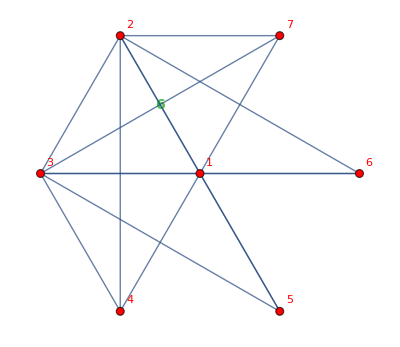
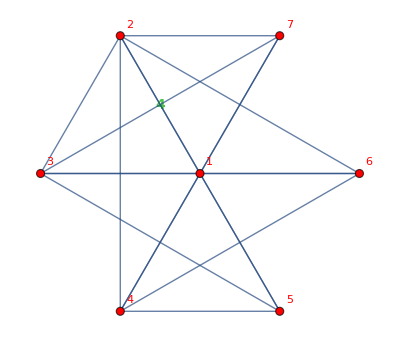
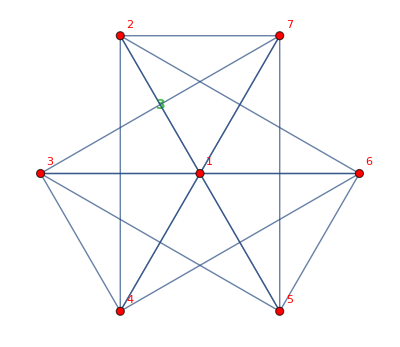

```mathematica
BarelyFourColorableGraphsOfCount[7]
```

```mathematica
sevenAlways={{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}
```

{{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}

```mathematica
Map[#->Map[If[MemberQ[sevenAlways,#],Style[#,Darker[Green]],#]&,FindPartitions[#]]&,BarelyFourColorableGraphsOfCount[7]]
```

{-Graphics-→{{4,1,1,1},{2,2,1,1,1},{3,1,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}},-Graphics-→{{3,2,1,1},{2,2,1,1,1},{3,1,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}},-Graphics-→{{2,2,2,1},{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}}

## Caalculate always

```mathematica
always7=Calcalways[doc7]
```

{{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}

```mathematica
Map[#->Map[If[MemberQ[always7,#],Style[#,Darker[Green]],#]&,FindPartitions[#]]&,BarelyFourColorableGraphsOfCount[7]]
```

{-Graphics-→{{4,1,1,1},{2,2,1,1,1},{3,1,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}},-Graphics-→{{3,2,1,1},{2,2,1,1,1},{3,1,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}},-Graphics-→{{2,2,2,1},{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}}

```mathematica
always8=Calcalways[doc8]
```

{{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

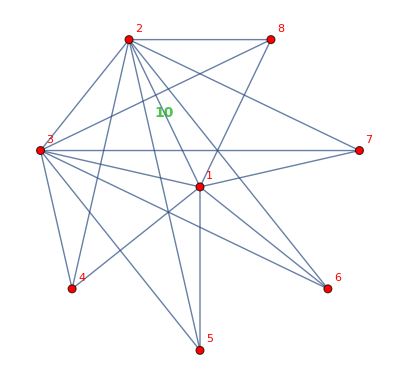
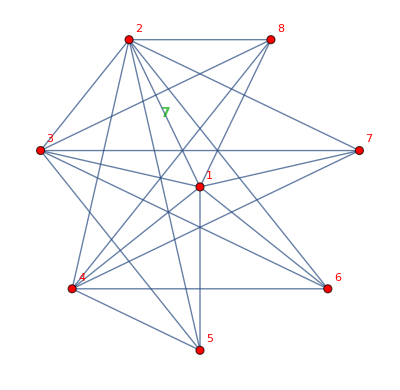
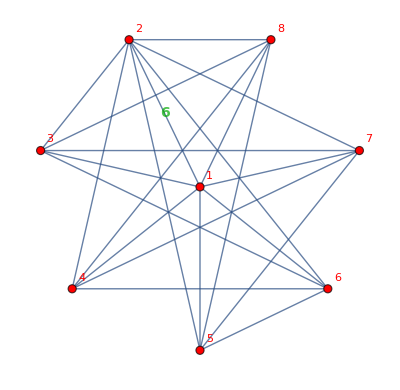
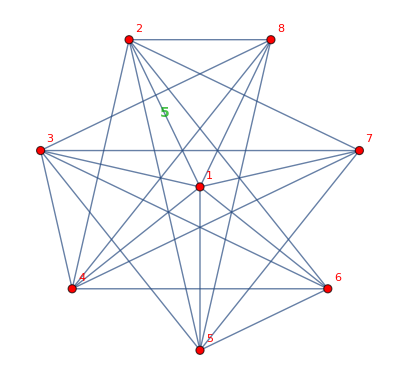
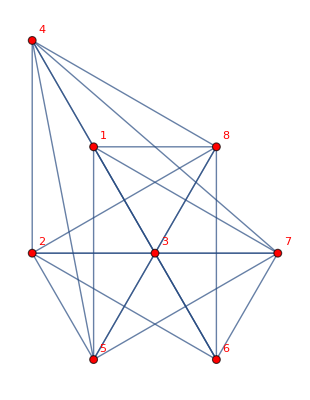
{-Graphics-→{{5,1,1,1},{3,2,1,1,1},{4,1,1,1,1},{2,2,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},-Graphics-→{{4,2,1,1},{2,2,2,1,1},{3,2,1,1,1},{4,1,1,1,1},{2,2,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},-Graphics-→{{3,3,1,1},{3,2,1,1,1},{2,2,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},-Graphics-→{{3,2,2,1},{2,2,2,1,1},{3,2,1,1,1},{2,2,1,1,1,1},{3,1,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},-Graphics-→{{2,2,2,2},{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}}

```mathematica
Map[#->Map[If[MemberQ[always8,#],Style[#,Darker[Green]],#]&,FindPartitions[#]]&,BarelyFourColorableGraphsOfCount[8]]
```

```mathematica
always9=Calcalways[doc9]
```

{{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
CalcBarely[parts_]:=Block[{always=Calcalways[parts],never=CalcNever[parts],n=Total[First[First[parts
]]]},Map[
With[{parts2=FindPartitions[#]},
Framed[Labeled[CompleteGraph[n,GraphHighlight->EdgeList[GraphComplement[#]],VertexLabels->"Name", GraphHighlightStyle->"Thick"],Grid[{{"size:",n},{"planar:",PlanarGraphQ[#]},{"maximalplanar:",MaximalPlanarQ[#]}},Frame->All]] ,FrameStyle->Directive[Thick,
If[(Length[Intersection[always,parts2]]==Length[always])&&(Length[Intersection[never,parts2]]==0),Darker[Green],Red]]]
->
TableForm[Map[If[MemberQ[always,#],Style[#,Darker[Green]],If[MemberQ[never,#],Style[#,Red],#]]&,parts2], TableDepth->1]
]&,BarelyFourColorableGraphsOfCount[n]]]
```

```mathematica
First[doc6]
```

{{2,2,2},1}

```mathematica
Total[First[First[doc6]]]
```

6

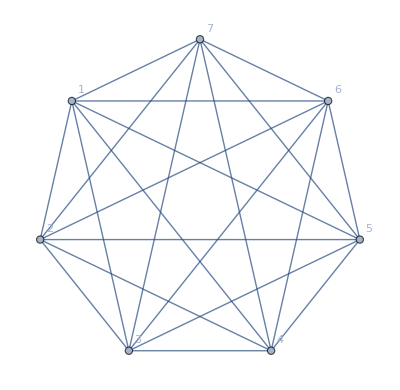
{-Graphics-size: | 7
planar: | False
maximalplanar: | False→{4,1,1,1}
{2,2,1,1,1}
{3,1,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1},-Graphics-size: | 7
planar: | False
maximalplanar: | False→{3,2,1,1}
{2,2,1,1,1}
{3,1,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1},-Graphics-size: | 7
planar: | False
maximalplanar: | False→{2,2,2,1}
{2,2,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1}}

```mathematica
CalcBarely[doc7]
```

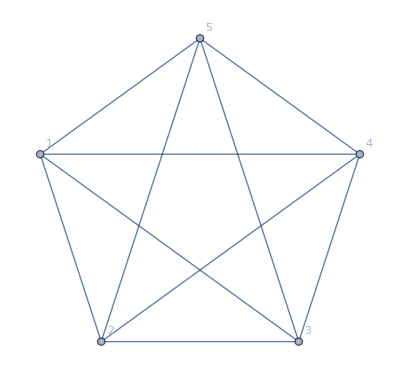
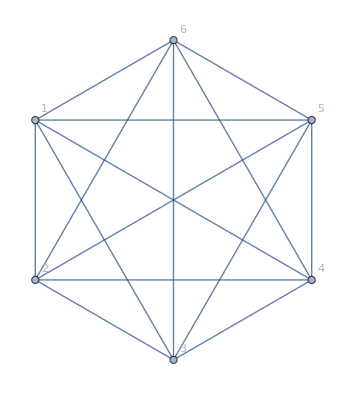
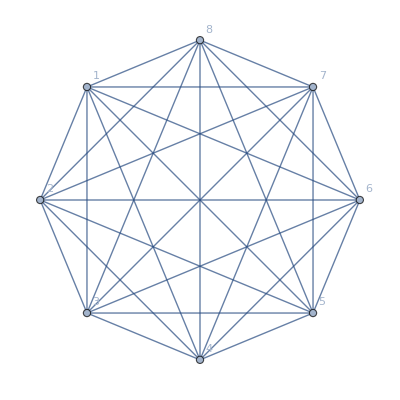
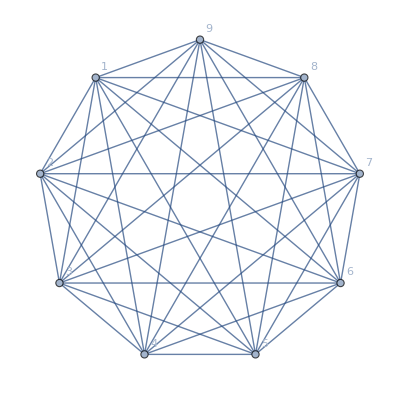
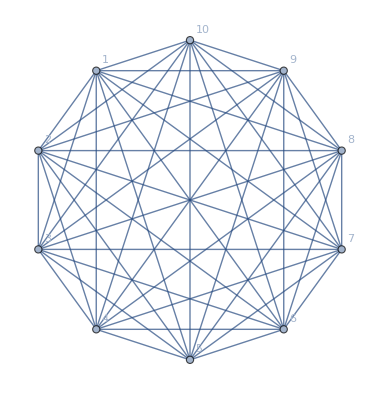
{{-Graphics-{size:,5,planar:,True,maximalplanar:,True}→{2,1,1,1}
{1,1,1,1,1}},{-Graphics-{size:,6,planar:,False,maximalplanar:,False}→{3,1,1,1}
{2,1,1,1,1}
{1,1,1,1,1,1},-Graphics-{size:,6,planar:,False,maximalplanar:,False}→{2,2,1,1}
{2,1,1,1,1}
{1,1,1,1,1,1}},{-Graphics-{size:,7,planar:,False,maximalplanar:,False}→{4,1,1,1}
{2,2,1,1,1}
{3,1,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1},-Graphics-{size:,7,planar:,False,maximalplanar:,False}→{3,2,1,1}
{2,2,1,1,1}
{3,1,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1},-Graphics-{size:,7,planar:,False,maximalplanar:,False}→{2,2,2,1}
{2,2,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1}},{-Graphics-{size:,8,planar:,False,maximalplanar:,False}→{5,1,1,1}
{3,2,1,1,1}
{4,1,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-{size:,8,planar:,False,maximalplanar:,False}→{4,2,1,1}
{2,2,2,1,1}
{3,2,1,1,1}
{4,1,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-{size:,8,planar:,False,maximalplanar:,False}→{3,3,1,1}
{3,2,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-{size:,8,planar:,False,maximalplanar:,False}→{3,2,2,1}
{2,2,2,1,1}
{3,2,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-{size:,8,planar:,False,maximalplanar:,False}→{2,2,2,2}
{2,2,2,1,1}
{2,2,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1}},{-Graphics-{size:,9,planar:,False,maximalplanar:,False}→{6,1,1,1}
{3,3,1,1,1}
{4,2,1,1,1}
{5,1,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-{size:,9,planar:,False,maximalplanar:,False}→{5,2,1,1}
{3,2,2,1,1}
{4,2,1,1,1}
{5,1,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-{size:,9,planar:,False,maximalplanar:,False}→{4,3,1,1}
{3,2,2,1,1}
{3,3,1,1,1}
{4,2,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-{size:,9,planar:,False,maximalplanar:,False}→{4,2,2,1}
{2,2,2,2,1}
{3,2,2,1,1}
{4,2,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-{size:,9,planar:,False,maximalplanar:,False}→{3,3,2,1}
{3,2,2,1,1}
{3,3,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-{size:,9,planar:,False,maximalplanar:,False}→{3,2,2,2}
{2,2,2,2,1}
{3,2,2,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1}},{-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{7,1,1,1}
{4,3,1,1,1}
{5,2,1,1,1}
{6,1,1,1,1}
{3,2,2,1,1,1}
{3,3,1,1,1,1}
{4,2,1,1,1,1}
{5,1,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{4,1,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{6,2,1,1}
{3,3,2,1,1}
{4,2,2,1,1}
{5,2,1,1,1}
{6,1,1,1,1}
{2,2,2,2,1,1}
{3,2,2,1,1,1}
{3,3,1,1,1,1}
{4,2,1,1,1,1}
{5,1,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{4,1,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{5,3,1,1}
{3,3,2,1,1}
{4,3,1,1,1}
{5,2,1,1,1}
{3,2,2,1,1,1}
{3,3,1,1,1,1}
{4,2,1,1,1,1}
{5,1,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{4,1,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{5,2,2,1}
{3,2,2,2,1}
{4,2,2,1,1}
{5,2,1,1,1}
{2,2,2,2,1,1}
{3,2,2,1,1,1}
{4,2,1,1,1,1}
{5,1,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{4,1,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{4,4,1,1}
{4,2,2,1,1}
{4,3,1,1,1}
{2,2,2,2,1,1}
{3,2,2,1,1,1}
{3,3,1,1,1,1}
{4,2,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{4,1,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{4,3,2,1}
{3,2,2,2,1}
{3,3,2,1,1}
{4,2,2,1,1}
{4,3,1,1,1}
{2,2,2,2,1,1}
{3,2,2,1,1,1}
{3,3,1,1,1,1}
{4,2,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{4,1,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{4,2,2,2}
{2,2,2,2,2}
{3,2,2,2,1}
{4,2,2,1,1}
{2,2,2,2,1,1}
{3,2,2,1,1,1}
{4,2,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{4,1,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{3,3,3,1}
{3,3,2,1,1}
{3,2,2,1,1,1}
{3,3,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1},-Graphics-{size:,10,planar:,False,maximalplanar:,False}→{3,3,2,2}
{3,2,2,2,1}
{3,3,2,1,1}
{2,2,2,2,1,1}
{3,2,2,1,1,1}
{3,3,1,1,1,1}
{2,2,2,1,1,1,1}
{3,2,1,1,1,1,1}
{2,2,1,1,1,1,1,1}
{3,1,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Table[CalcBarely[d],{d,{doc5,doc6,doc7,doc8,doc9,doc10}}]
```

{{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

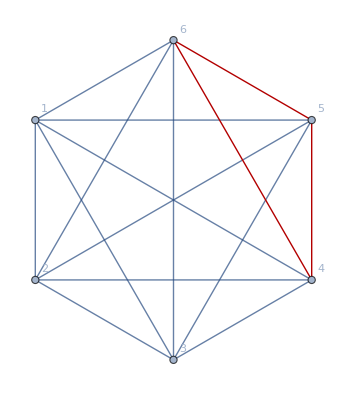
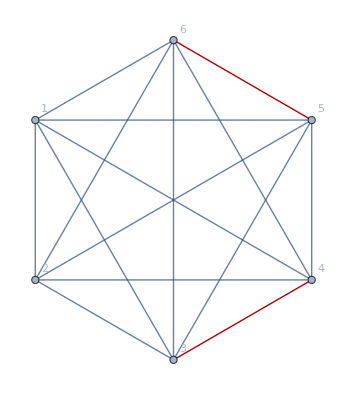
{-Graphics-→3 | 1 | 1 | 1
{2,1,1,1,1} |  |  | 
{1,1,1,1,1,1} |  |  | ,-Graphics-→{2,2,1,1}
{2,1,1,1,1}
{1,1,1,1,1,1}}

```mathematica
CalcBarely[doc6]
```

{{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}

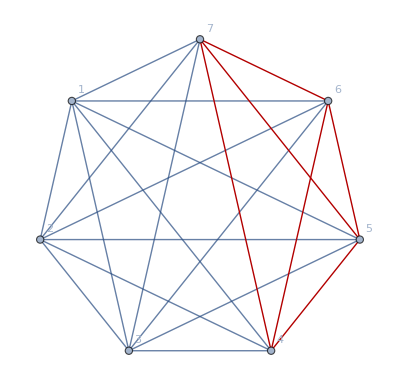
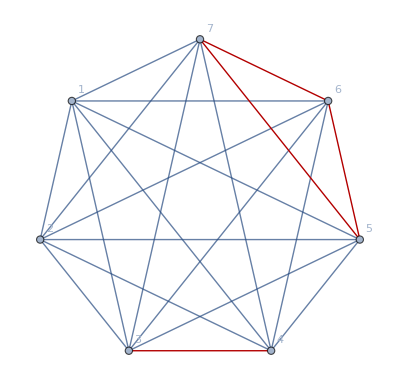
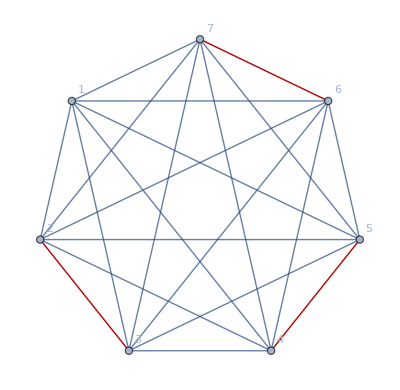
{-Graphics-→{4,1,1,1}
{2,2,1,1,1}
{3,1,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1},-Graphics-→{3,2,1,1}
{2,2,1,1,1}
{3,1,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1},-Graphics-→{2,2,2,1}
{2,2,1,1,1}
{2,1,1,1,1,1}
{1,1,1,1,1,1,1}}

```mathematica
CalcBarely[doc7]
```

{{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

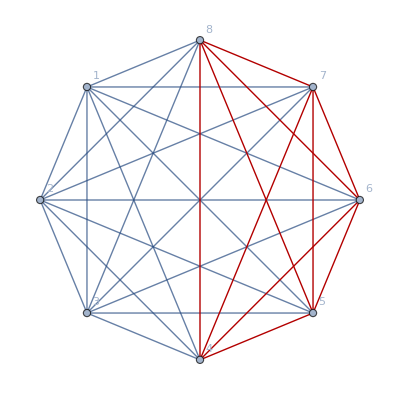
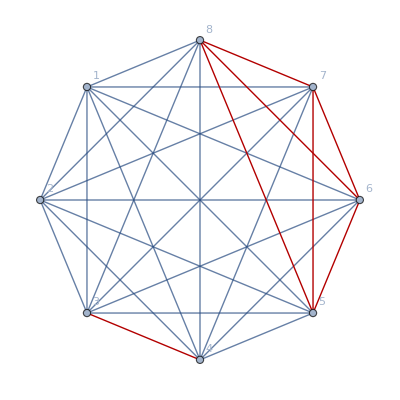
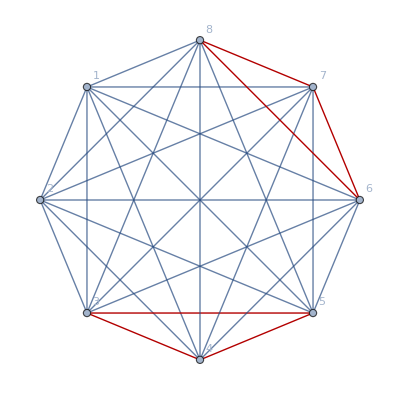
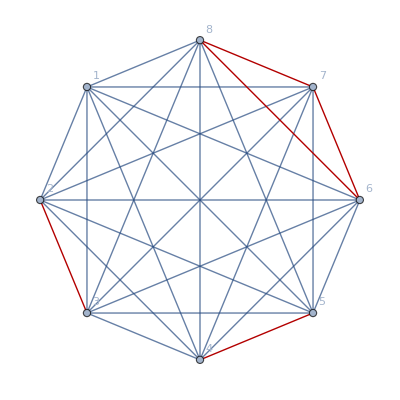
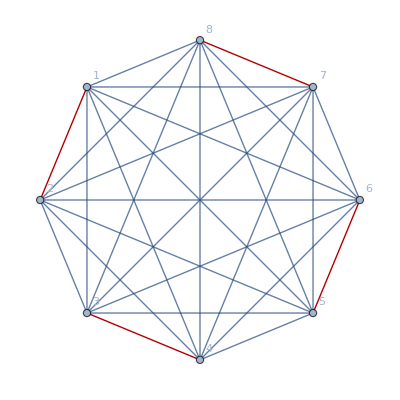
{-Graphics-→{5,1,1,1}
{3,2,1,1,1}
{4,1,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-→{4,2,1,1}
{2,2,2,1,1}
{3,2,1,1,1}
{4,1,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-→{3,3,1,1}
{3,2,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-→{3,2,2,1}
{2,2,2,1,1}
{3,2,1,1,1}
{2,2,1,1,1,1}
{3,1,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1},-Graphics-→{2,2,2,2}
{2,2,2,1,1}
{2,2,1,1,1,1}
{2,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1}}

```mathematica
CalcBarely[doc8]
```

{{3,2,2,1,1},{2,2,2,1,1,1},{3,2,1,1,1,1},{2,2,1,1,1,1,1},{3,1,1,1,1,1,1},{2,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1}}

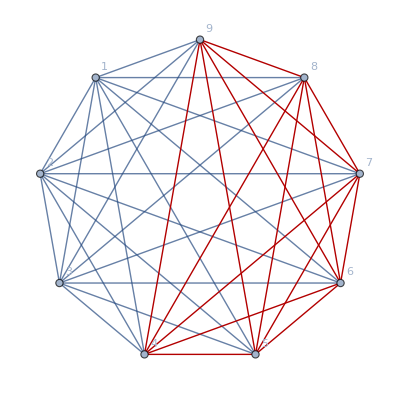
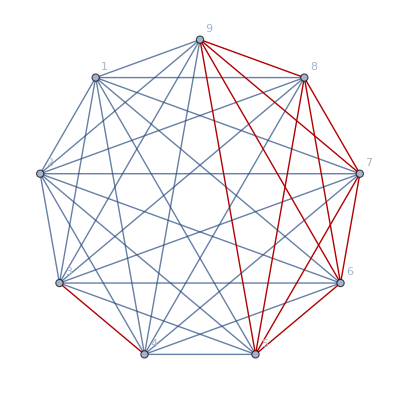
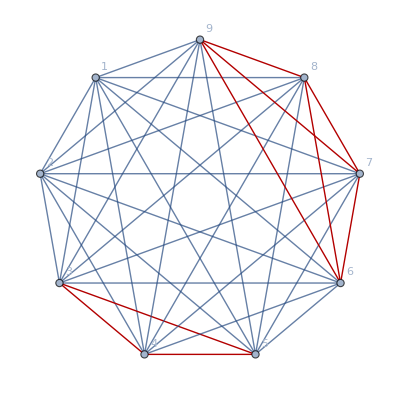
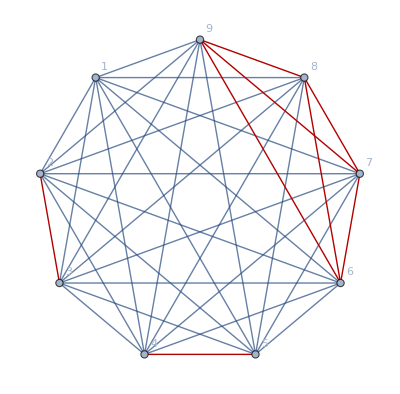
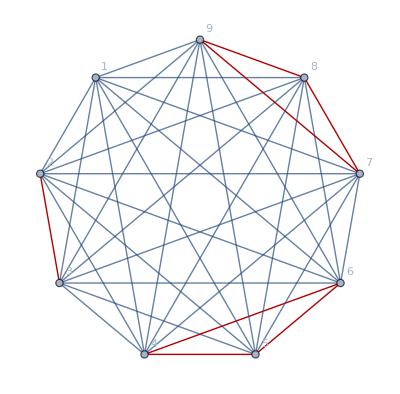
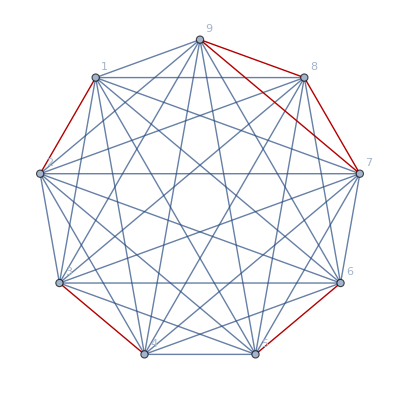
{-Graphics-→{6,1,1,1}
{3,3,1,1,1}
{4,2,1,1,1}
{5,1,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-→{5,2,1,1}
{3,2,2,1,1}
{4,2,1,1,1}
{5,1,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-→{4,3,1,1}
{3,2,2,1,1}
{3,3,1,1,1}
{4,2,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-→{4,2,2,1}
{2,2,2,2,1}
{3,2,2,1,1}
{4,2,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{4,1,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-→{3,3,2,1}
{3,2,2,1,1}
{3,3,1,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1},-Graphics-→{3,2,2,2}
{2,2,2,2,1}
{3,2,2,1,1}
{2,2,2,1,1,1}
{3,2,1,1,1,1}
{2,2,1,1,1,1,1}
{3,1,1,1,1,1,1}
{2,1,1,1,1,1,1,1}
{1,1,1,1,1,1,1,1,1}}

```mathematica
CalcBarely[doc9]
```

```mathematica
CalcBarely[6,doc6]
```